Определим граф как неориентированный для первой задачи

```mathematica
Ed={{1,2,1},{1,3,7},{1,4,8},{1,6,3},{2,5,3},{2,7,9},{3,4,8},{4,9,8},{5,8,6},{6,11,9},{7,3,2},{7,6,9},{7,8,1},{8,9,7},{8,13,5},{9,11,10},{9,13,7},{9,14,1},{11,13,9},{11,14,3},{13,16,4},{13,17,5},{14,18,7},{14,19,9},{16,17,10},{16,18,9},{17,20,2},{18,20,7},{19,5,7},{19,20,7}};
vertices=Union[Flatten[Ed[[All,{1,2}]]]];
edges=UndirectedEdge@@@Ed[[All,{1,2}]];
weights=Ed[[All,3]];
```

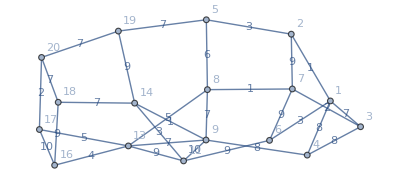

```mathematica
g=Graph[vertices,edges,EdgeWeight->weights,EdgeLabels->"EdgeWeight",VertexLabels->Automatic]

(*Определяем ребро e*)
e=UndirectedEdge[9,11];
```

Для гарантии включения ребра e, заменим его вес на нулевой.

```mathematica
adjustedWeights=ReplacePart[weights,Position[edges,e][[1]]->0];

(*Обновляем граф с новыми весами*)
adjustedGraph=Graph[vertices,edges,EdgeWeight->adjustedWeights,EdgeLabels->"EdgeWeight"];
```

```mathematica
(*Находим минимальный остов*)
spanningTree=FindSpanningTree[adjustedGraph,EdgeWeight->adjustedWeights];
```

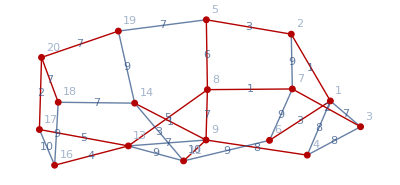

```mathematica
(*Отображение результата*)
HighlightGraph[g,spanningTree]
```

```mathematica
diredges = DirectedEdge@@@Ed[[All,{1,2}]];
```

Определим граф как ориентированный для второй задачи

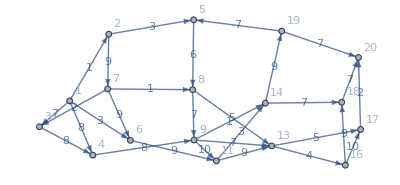

```mathematica
g2=Graph[vertices,diredges,EdgeWeight->weights,EdgeLabels->"EdgeWeight",VertexLabels->Automatic]
```

Найдем компоненты сильной связности графа с помощью встроенной функции

```mathematica
scc= ConnectedComponents[g2]
```

{{20},{17},{18},{16},{13},{5,8,9,11,14,19},{4},{3},{6},{7},{2},{1}}

```mathematica
(*Строим фактор-граф:каждая компонента становится одной вершиной*)
```

```mathematica
factors=Table[Subscript[f,i],{i,Length[Ed]}];

(*Генерируем фактор-граф*)
factorEdges=Flatten[Table[{Ed[[i,1]]->factors[[i]],factors[[i]]->Ed[[i,2]]},{i,Length[Ed]}]];
```

```mathematica
factorGraph=Graph[Union[Flatten[Ed[[All,{1,2}]]],factors],factorEdges,VertexLabels->"Name",EdgeStyle->Arrowheads[0.02],GraphStyle->"Name"]
```

-Graphics-